```mathematica
(* 多核计算指令 *)
Evaluate[5!]
```

120

```mathematica
ParallelEvaluate[5!]
```

{120,120,120,120,120,120,120,120}

```mathematica
ParallelEvaluate[a=5;a^2]
```

{25,25,25,25,25,25,25,25}

```mathematica
ParallelEvaluate[a=RandomReal[];a^2]
```

{0.233946,0.00244154,0.509815,0.178742,0.312996,0.236237,0.615006,0.412965}

```mathematica
ParallelEvaluate[a=RandomReal[{0,1},{5,1}];Mean[a]]
```

{{0.32804},{0.384324},{0.741354},{0.559278},{0.396302},{0.569034},{0.599089},{0.592815}}

```mathematica
Mean[ParallelEvaluate[a=RandomReal[{0,1},{5,1}]]]
```

{{0.64375},{0.592029},{0.487278},{0.574927},{0.455005}}

```mathematica
(* 使用多个内核进行仿真 *)
sampleSize=10^3;
myList = RandomReal[{-1,1},{sampleSize,2}];
myPattern[pair_]:=pair[[1]]^2+pair[[2]]^2<1;
myResult=Select[myList,myPattern];
```

```mathematica
N[Length[myResult]/Length[myList]]
```

0.803

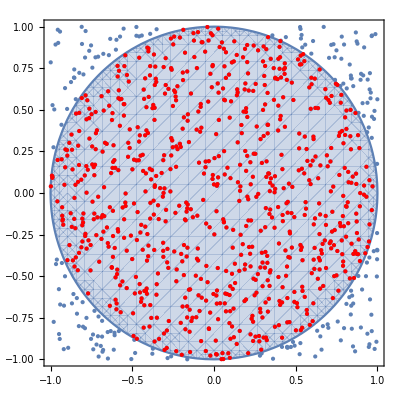

```mathematica
(* 显示所有的采样点，使得不等式成立的点被标记为红色 *)
Show[
RegionPlot[x^2+y^2<=1,{x,-1,1},{y,-1,1}],
ListPlot[myList,PlotStyle->{PointSize[Small]}],
ListPlot[myResult,PlotStyle->{Red,PointSize[Small]}]
]
```

```mathematica
(* 使用并行计算 *)
ParallelEvaluate[
sampleSize=10^3;
myList=RandomReal[{-1,1},{sampleSize,2}];
myPattern[pair_]:=pair[[1]]^2+pair[[2]]^2<1;
myResult=Select[myList,myPattern];
N[Length[myResult]/Length[myList]]
]
```

{0.785,0.777,0.767,0.77,0.774,0.796,0.773,0.794}

```mathematica
(* 使用并行计算求出随机数以后，使用主内核对得到的值计算平均数 *)
ParallelEvaluate[
sampleSize=10^3;
myList=RandomReal[{-1,1},{sampleSize,2}];
myPattern[pair_]:=pair[[1]]^2+pair[[2]]^2<1;
myResult=Select[myList,myPattern];
N[Length[myResult]/Length[myList]]
] // Mean
```

0.7835

```mathematica
(* 并行计算的其他指令 *)
Table[Solve[x^i==y,x],{i,1,5,1}]
```

{{{x→y}},{{x→-√y},{x→√y}},{{x→y^(1/3)},{x→-(-1)^(1/3) y^(1/3)},{x→(-1)^(2/3) y^(1/3)}},{{x→-y^(1/4)},{x→-ⅈ y^(1/4)},{x→ⅈ y^(1/4)},{x→y^(1/4)}},{{x→y^(1/5)},{x→-(-1)^(1/5) y^(1/5)},{x→(-1)^(2/5) y^(1/5)},{x→-(-1)^(3/5) y^(1/5)},{x→(-1)^(4/5) y^(1/5)}}}

```mathematica
ParallelTable[Solve[x^i==5y,x],{i,1,5,1}]
```

{{{x→5 y}},{{x→-√5 √y},{x→√5 √y}},{{x→-(-5)^(1/3) y^(1/3)},{x→5^(1/3) y^(1/3)},{x→(-1)^(2/3) 5^(1/3) y^(1/3)}},{{x→-5^(1/4) y^(1/4)},{x→-ⅈ 5^(1/4) y^(1/4)},{x→ⅈ 5^(1/4) y^(1/4)},{x→5^(1/4) y^(1/4)}},{{x→-(-5)^(1/5) y^(1/5)},{x→5^(1/5) y^(1/5)},{x→(-1)^(2/5) 5^(1/5) y^(1/5)},{x→-(-1)^(3/5) 5^(1/5) y^(1/5)},{x→(-1)^(4/5) 5^(1/5) y^(1/5)}}}

```mathematica
(* 计算程序执行的时间 *)
AbsoluteTiming[Table[Length[Solve[x^i==y,x]],{i,1,500,1}]]
```

{0.943189,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500}}

```mathematica
AbsoluteTiming[ParallelTable[Length[Solve[x^i==y,x]],{i,1,500,1}]]
```

{0.23744,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500}}

```mathematica
(* 对可并行计算的计算过程进行并行化封装 *)
Parallelize[
Table[Length[Solve[x^i==5y,x]],{i,1,500,1}]
]//Short
```

{1,2,3,4,5,6,7,8,9,10,11,12,«476»,489,490,491,492,493,494,495,496,497,498,499,500}

```mathematica
Parallelize[∫1/(x^6+1)ⅆx]
```

Parallelize::nopar1: ∫1/(x^6+1)ⅆx cannot be parallelized; proceeding with sequential evaluation.

1/12 (-2 ArcTan[√3-2 x]+4 ArcTan[x]+2 ArcTan[√3+2 x]-√3 Log[1-√3 x+x^2]+√3 Log[1+√3 x+x^2])

```mathematica
(* 在大型程序上使用并行指令 *)
dataFitApp[data_,polydegree_]:=
(
fits=Table[LinearModelFit[data,Table[x^j,{j,0,i}],x],{i,1,polydegree}];
Table[
	Show[
	ListPlot[data,PlotStyle->PointSize[Medium]],
	Plot[fits[[i]]["BestFit"],{x,0,100},PlotStyle->Red],
	PlotLabel->"degree"<>ToString[i]<>" polynomial"<>"\n"<>"r^2:"<>ToString[fits[[i]]["RSquared"]]],
	{i,polydegree}
]
);
```

```mathematica
data1 = QuantityMagnitude[Normal[CountryData["Sweden",{{"GDP"},{1970,2010}}]][[All,2]]];
```

```mathematica
data1[1;;10]
```

{3.80925×10^10,4.15664×10^10,4.89541×10^10,5.9405×10^10,6.60133×10^10,8.28854×10^10,8.93621×10^10,9.44687×10^10,1.04442×10^11,1.23386×10^11,1.42092×10^11,1.29687×10^11,1.14381×10^11,1.05014×10^11,1.09201×10^11,1.14124×10^11,1.50498×10^11,1.8301×10^11,2.06987×10^11,2.17948×10^11,2.61846×10^11,2.74229×10^11,2.84321×10^11,2.12953×10^11,2.29034×10^11,2.67306×10^11,2.91744×10^11,2.68146×10^11,2.70809×10^11,2.74072×10^11,2.62835×10^11,2.42396×10^11,2.66849×10^11,3.34337×10^11,3.85118×10^11,3.92218×10^11,4.23093×10^11,4.91253×10^11,5.17706×10^11,4.36537×10^11,4.95813×10^11}[1;;10]

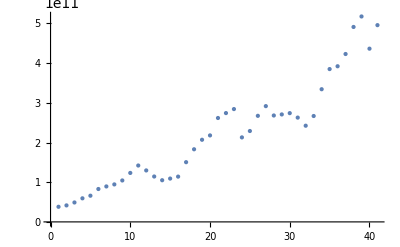

```mathematica
ListPlot[data1,PlotStyle->PointSize[Medium]]
```

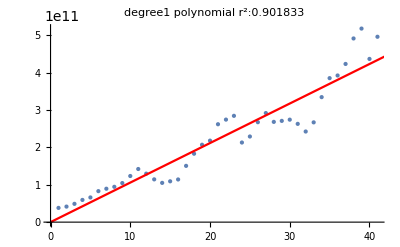
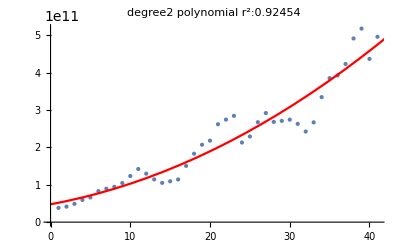
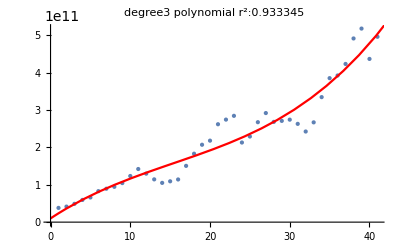
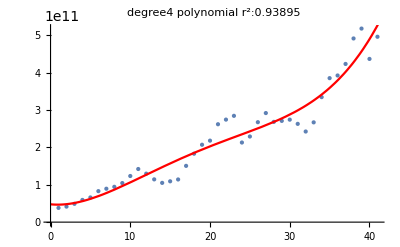
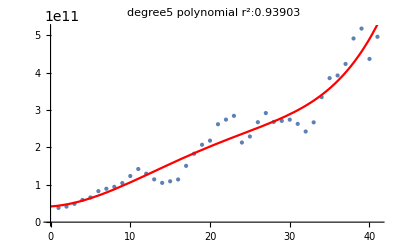
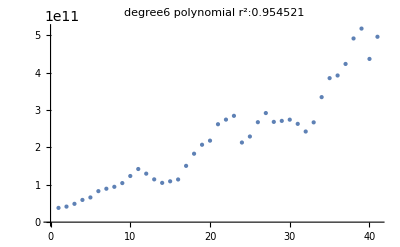
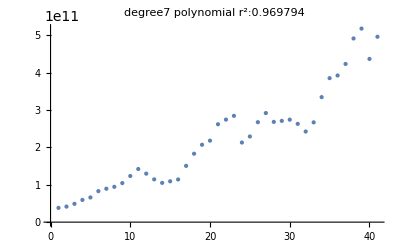
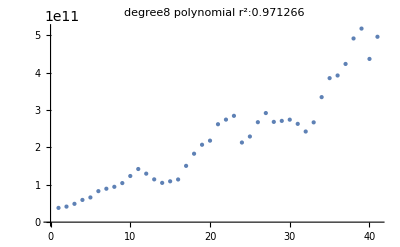

```mathematica
dataFitApp[data1,8]
```

```mathematica
(* 在大型程序上使用并行指令 *)
parralleladataFitApp[data_,polydegree_]:=
(
fits=Table[LinearModelFit[data,Table[x^j,{j,0,i}],x],{i,1,polydegree}];
ParallelTable[
	Show[
	ListPlot[data,PlotStyle->PointSize[Medium]],
	Plot[fits[[i]]["BestFit"],{x,0,100},PlotStyle->Red],
	PlotLabel->"degree"<>ToString[i]<>" polynomial"<>"\n"<>"r^2:"<>ToString[fits[[i]]["RSquared"]]],
	{i,polydegree}
]
);
```

```mathematica
parralleladataFitApp[data1,8]; // AbsoluteTiming
```

{0.479281,Null}

```mathematica
dataFitApp[data1,8]; // AbsoluteTiming
```

{0.519326,Null}

```mathematica
(* CUDA *)
```

```mathematica
Needs["CUDALink`"]
```

GetCUDAToolkitRoot::nocuda: Could not find NVIDIA CUDA Toolkit.

DirectoryName::string: DirectoryName[$Failed] 中位置 1 处应该是字符串.

CUDACompileTools`FindCUDAToolkit`GetCUDAToolkitRoot::nocuda: Could not find NVIDIA CUDA Toolkit.

LibraryFunctionLoad::noform: D:\Mathematica\13.1\SystemFiles\Components\CUDACompileTools\LibraryResources\Windows-x86-64\CUDAExtensions.dll cannot be loaded as a structured library created by the Wolfram Compiler.

Lookup::invrl: 参数 $Failed 不是一个有效的 Association 或规则列表.

Lookup::luarg: Lookup[CUDACompileTools`$CUDAExtensionsLibraryFunctions,CUDAStart][0] 含有一个不准确的参数数目.

Lookup::invrl: 参数 $Failed 不是一个有效的 Association 或规则列表.

General::stop: 在本次计算中，Lookup::invrl 的进一步输出将被抑制.

```mathematica
CUDAQ[]
```

False

False